# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at x=0.

```mathematica
Needs["NDSolve`FEM`"]
```

#### Parameters xs=1, λ=1, k1, k2, Dg = sg^2/2, Dξ = σξ^2/2 , x0, xh0

```mathematica
FP= D[p[x,xh,  t], t]== λ*xh*D[p[x,xh, t], x] -k2 *x*D[p[x,xh,t], xh]+k1*D[xh*p[x, xh, t], xh]+Dg*D[p[x, xh, t], {x, 2}]+Dξ*k2^2*D[p[x, xh, t], {xh, 2}]
```

p^(0,0,1)[x,xh,t]==-k2 x p^(0,1,0)[x,xh,t]+k1 (p[x,xh,t]+xh p^(0,1,0)[x,xh,t])+Dξ k2^2 p^(0,2,0)[x,xh,t]+xh λ p^(1,0,0)[x,xh,t]+Dg p^(2,0,0)[x,xh,t]

#### Boundary conditions p(1, xh, t) = 0, dp/dxh (x, 0, t)=0, p(x, infinity, t)=0, p(infinity, xh, t)=0 Initial condition p(x0, xh0, 0) = d(x-x0)d(xh-xh0) k2=σg/(λ σt)*k1

```mathematica
soltry1= (p/.NDSolve[{(FP/.{λ->0.5, Dg->1, Dξ->0.04, k1->1, k2->Sqrt[1/0.04]/0.5*1}),
	                 p[x,xh, 0]== PDF[MultinormalDistribution[{5, 5},{{Dg/k1+(Dg*k1)/(k2 λ)+k2 λ Dξ/k1,Dg/λ},{Dg/λ,(k2 (Dg+k2 λ Dξ))/(k1* λ)}}/.{λ->0.5, Dg->1, Dξ->0.04, k1->5, k2->Sqrt[1/0.04]/0.5*5}], {x, xh}],
			p[1, xh, t]==0,
                            p[12, xh, t]==0,
                            p[x, 12, t]==0,
                      p[x, 0, t]==0
			(* D[p[x, xh, t], xh]==NeumannValue[0, xh==0]*)
(*(D[p[x, xh, t], xh] /.xh->0)==0*)
                           }, 
                                   p,{t,0,4},{x, 1,12},{xh, 0,12}, 
Method->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->"TensorProductGrid"}])[[1]]
Manipulate[Plot3D[soltry1[x, xh, t], {x, 1, 12}, {xh, 0, 12}, PlotRange->{-0.1, 0.1}], {t, 0, 4}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

InterpolatingFunction[{{1., 12.}, {0., 12.}, {0., 4.}}, <>]

```mathematica
soltry2= (p/.NDSolve[{(FP/.{λ->1, Dg->1, Dξ->0.04, k1->5, k2->5}),
	                 p[x,xh, 0]== PDF[MultinormalDistribution[{5, 5},{{Dg/k1+(Dg*k1)/(k2 λ)+k2 λ Dξ/k1,Dg/λ},{Dg/λ,(k2 (Dg+k2 λ Dξ))/(k1* λ)}}/.{λ->1, Dg->1, Dξ->0.04, k1->5, k2->5}], {x, xh}],
			p[1, xh, t]==0,
                            p[12, xh, t]==0,
                            p[x, 12, t]==0,
                      p[x, 0, t]==0
			(* D[p[x, xh, t], xh]==NeumannValue[0, xh==0]*)
(*(D[p[x, xh, t], xh] /.xh->0)==0*)
                           }, 
                                   p,{t,0,4},{x, 1,12},{xh, 0,12}, 
Method->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->"TensorProductGrid"}])[[1]]
Manipulate[Plot3D[soltry2[x, xh, t], {x, 1, 12}, {xh, 0, 12}, PlotRange->{-0.1, 1}], {t, 0, 4}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

InterpolatingFunction[{{1., 12.}, {0., 12.}, {0., 4.}}, <>]

```mathematica
soltry3= (p/.NDSolve[{(FP/.{λ->2, Dg->1, Dξ->0.04, k1->5, k2->5}),
	                 p[x,xh, 0]== PDF[MultinormalDistribution[{5, 5},{{Dg/k1+(Dg*k1)/(k2 λ)+k2 λ Dξ/k1,Dg/λ},{Dg/λ,(k2 (Dg+k2 λ Dξ))/(k1* λ)}}/.{λ->2, Dg->1, Dξ->0.04, k1->5, k2->5}], {x, xh}],
			p[1, xh, t]==0,
                            p[12, xh, t]==0,
                            p[x, 12, t]==0,
                      p[x, 0, t]==0
			(* D[p[x, xh, t], xh]==NeumannValue[0, xh==0]*)
(*(D[p[x, xh, t], xh] /.xh->0)==0*)
                           }, 
                                   p,{t,0,4},{x, 1,12},{xh, 0,12}, 
Method->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->"TensorProductGrid"}])[[1]]
Manipulate[Plot3D[soltry3[x, xh, t], {x, 1, 12}, {xh, 0, 12}, PlotRange->{-0.1, 1}], {t, 0, 4}]
```

InterpolatingFunction[{{1., 12.}, {0., 12.}, {0., 4.}}, <>]

## Integrate to get survival probability

```mathematica
S1[t] = Integrate[soltry1[x, xh, t], {x, 1, 12}, {xh, 0, 12}] ;
S2[t] = Integrate[soltry2[x, xh, t], {x, 1, 12}, {xh, 0, 12}] ;
S3[t] = Integrate[soltry3[x, xh, t], {x, 1, 12}, {xh, 0, 12}] ;
```

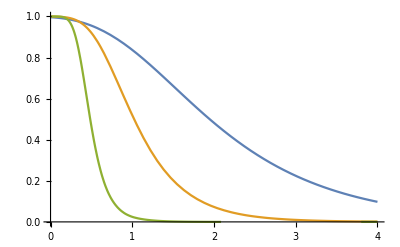

```mathematica
Plot[{S1[t], S2[t], S3[t]}, {t, 0, 4}, PlotRange->{0, 1}]
```

## Get first-passage time probability

```mathematica
f1[t] =FullSimplify[-D[S1[t], t]];
f2[t] =FullSimplify[-D[S2[t], t]];
f3[t] =FullSimplify[-D[S3[t], t]]
```

-InterpolatingFunction[…][t]

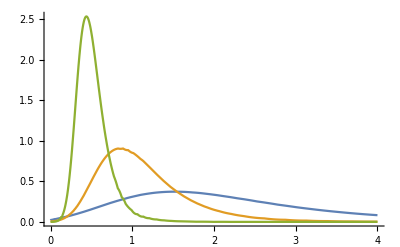

```mathematica
Plot[{f1[t],f2[t], f3[t]}, {t, 0,4}, PlotRange->All]
```

```mathematica
NIntegrate[t*f1[t], {t, 0, 4}]
NIntegrate[t*f2[t], {t, 0, 4}]
NIntegrate[t*f3[t], {t, 0, 4}]
```

1.70531

1.12048

0.51771

```mathematica
NIntegrate[t^2*f1[t], {t, 0, 4}]
NIntegrate[t^2*f2[t], {t, 0, 4}]
NIntegrate[t^2*f3[t], {t, 0, 4}]
```

3.98208

1.55488

0.306953

## Plots and scaling

## Behavior with v near crossover

```mathematica
x0Constant = 2
vCrossover = N[x0Constant*Erfc[x0Constant]]
vRange = Reverse[N[PowerRange[5*^-5,2*^-2 , 3]]]
 DConstant = 0.5
 kConstant = 1
```

2

0.00935547

{0.01215,0.00405,0.00135,0.00045,0.00015,0.00005}

0.5

1

```mathematica
results =FPT[DConstant,kConstant, x0Constant, #]&/@vRange
```

General::munfl: -5.07352×10^-307 (-0.0140515) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.07352×10^-307 0.0140515 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.07352×10^-307 (-0.00702576) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

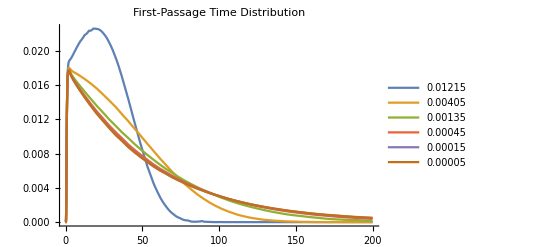

```mathematica
Plot[results, {t, 0, 200}, PlotRange->All, PlotLegends->vRange, PlotLabel->"First-Passage Time Distribution"]
```

## Behavior with x0 near crossover

```mathematica
x0Range = Range[1, 7, 1]
vConstant = 1*^-3
x0Crossover = FindRoot[vConstant - x*(1-Erf[x]), {x, 2}]
 DConstant = 0.5
kConstant = 1
```

{1,2,3,4,5,6,7}

1/1000

{x→2.50348}

0.5

1

```mathematica
results =FPT[DConstant,kConstant, #, vConstant]&/@x0Range
```

General::munfl: 3.29208×10^-306 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.93187×10^-308 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -4.08071×10^-308 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

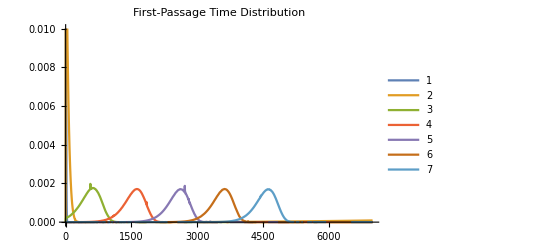

```mathematica
Plot[results, {t, 0, 7000}, PlotLegends->x0Range, PlotLabel->"First-Passage Time Distribution", PlotRange->{0, 0.01}]
```

#### Scaling with D

```mathematica
Clear[x0, d, v, k]
vConstant = 0.01
 DRange = PowerRange[0.1, 45, 2.7]
 kConstant = 1
x0Constant = 15
DCrossover = NSolve[(x0Constant/vConstant )== 1/Erfc[Sqrt[kConstant/(2*d)]*x0Constant], d]
```

0.01

{0.1,0.27,0.729,1.9683,5.31441,14.3489,38.742}

1

15

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{d→19.4301}}

```mathematica
results =FPT[#,kConstant, x0Constant, vConstant]&/@DRange
```

General::munfl: -9.57366×10^-308 (-0.00747168) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.57366×10^-308 0.00747168 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.57366×10^-308 (-0.00373584) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

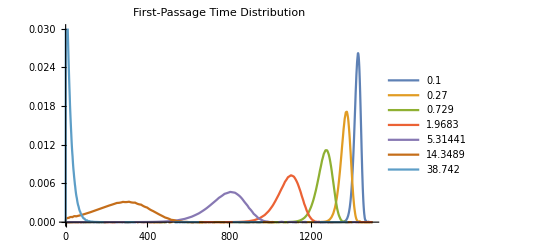

```mathematica
Plot[results, {t, 0, 1500}, PlotLegends->DRange, PlotLabel->"First-Passage Time Distribution", PlotRange->{0, 0.03}]
```